```mathematica
DSolve[{sx'[t]==-k1(sz sx[t]-sx[t])-kdeg(1-sx[t])},{sx[t]},t]
```

{{sx[t]→-(ⅇ^(k1 t+kdeg t-k1 sz t-(k1+kdeg-k1 sz) t) kdeg)/(-kdeg+k1 (-1+sz))+ⅇ^(k1 t+kdeg t-k1 sz t) C[1]}}

```mathematica
Solve[%1[[1]]/.Rule->Equal/.t->0,C[1]]
```

{{C[1]→kdeg/(-kdeg+k1 (-1+sz))+sx[0]}}

```mathematica
Solve[%2[[1]]/.Rule->Equal/.%1[[1]],sx[0]]
```

{{sx[0]→(kdeg+k1 C[1]+kdeg C[1]-k1 sz C[1])/(k1+kdeg-k1 sz)}}

```mathematica
FullSimplify[%1[[1]]/.Rule->Equal/.%2[[1]],Assumptions->{k1>0,kdeg>0,t>0}]
```

{sx[t]==(kdeg+ⅇ^((k1+kdeg-k1 sz) t) (-kdeg+(k1+kdeg-k1 sz) sx[0]))/(k1+kdeg-k1 sz)}

```mathematica
FullSimplify[Solve[%10[[1]],sx[0]],Assumptions->{k1>0,kdeg>0,t>0}]
```

Solve::naqs: 10 is not a quantified system of equations and inequalities.

Solve[10,sx[0]]

```mathematica
g[sx_,sz_,k1_,kdeg_,t_,x10_]:=((ⅇ^(-(k1+kdeg-k1 sz) t) (kdeg-ⅇ^((k1+kdeg-k1 sz) t) kdeg-(k1+kdeg-k1 sz) sx))/(-kdeg+k1 (-1+sz)))^x10
```

```mathematica
Needs["NumericalCalculus`"]
```

```mathematica
nmax=30;
```

```mathematica
mean=D[g[1,sz,10.1,0.5,1.4,1],{sz,1}]/.sz->1
```

10.169

```mathematica
std=√(D[Log[g[1,ⅇ^t,10.1,0.5,1.4,1]],{t,2}]/.t->0)
```

5.82325

```mathematica
origin=-1;
```

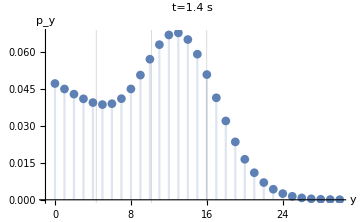

```mathematica
plot=DiscretePlot[SeriesCoefficient[NSeries[g[1,sz,10.1,0.5,1.4,1],{sz,0,nmax}],{sz,0,n}]//Re,{n,0,nmax},GridLines->{{{mean,Thick},{mean-std,{Thick,Dashed}},{mean+std,{Thick,Dashed}}},None},AxesLabel->{"y","p_y"},AxesOrigin->{origin,0},PlotRange->All,ImageSize->Medium,BaseStyle->{FontSize->18},PlotMarkers->Automatic,PlotLabel->"t=1.4 s"]
```

```mathematica
Export[NotebookDirectory[]<>"../bilder/gbdcatwithdeg.pdf",plot]
```

/home/matze/Paper/code/../bilder/gbdcatwithdeg.pdf

```mathematica
(* Normalization: *)
```

```mathematica
g[1,1,k1,kdeg,t,x10]
```

1

```mathematica
(* Solves the PDE *)
```

```mathematica
Simplify[{D[g[sx,sz,k1,kdeg,t,x10], t]==+k1(sz sx-sx)D[g[sx,sz,k1,kdeg,t,x10], sx]+kdeg(1-sx)D[g[sx,sz,k1,kdeg,t,x10], sx]},Assumptions->{k1>0,kdeg>0,t>0}]
```

{True}

```mathematica
gpoiss[sx_,sz_,k1_,kdeg_,t_,x10_]:=Exp[x10((ⅇ^(-(k1+kdeg-k1 sz) t) (kdeg-ⅇ^((k1+kdeg-k1 sz) t) kdeg-(k1+kdeg-k1 sz) sx))/(-kdeg+k1 (-1+sz))-1)+0.001(sz-1)]
```

```mathematica
gpoiss[1,1,k1,kdeg,t,x10]
```

1.

```mathematica
Simplify[{D[gpoiss[sx,sz,k1,kdeg,t,x10], t]==k1(sz sx-sx)D[gpoiss[sx,sz,k1,kdeg,t,x10], sx]+kdeg(1-sx)D[gpoiss[sx,sz,k1,kdeg,t,x10], sx]},Assumptions->{k1>0,kdeg>0,t>0}]
```

{True}

```mathematica
meanpoiss=D[gpoiss[1,sz,10.1,0.5,1.4,1],{sz,1}]/.sz->1
```

10.17

```mathematica
stdpoiss=√(D[Log[gpoiss[1,ⅇ^t,10.1,0.5,1.4,1]],{t,2}]/.t->0)
```

11.7183

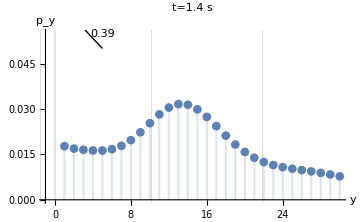

```mathematica
plot=Show[DiscretePlot[SeriesCoefficient[NSeries[gpoiss[1,sz,10.1,0.5,1.4,1],{sz,0,nmax}],{sz,0,n}]//Re,{n,0,nmax},GridLines->{{{meanpoiss,Thick},{meanpoiss-stdpoiss,{Thick,Dashed}},{meanpoiss+stdpoiss,{Thick,Dashed}}},None},AxesLabel->{"y","p_y"},PlotRange->Automatic,PlotMarkers->Automatic,ImageSize->Medium,BaseStyle->{FontSize->18},AxesOrigin->{origin,0},PlotLabel->"t=1.4 s"],Graphics[Arrow[{{5,0.05},{0.5,0.065}}]],Graphics[Text[ToString[NumberForm[gpoiss[1,sz,10.1,0.5,1.4,1]/.sz->0,2]],{5,0.053},{0,-2}]]]
```

```mathematica
Export[NotebookDirectory[]<>"../bilder/DCPcatwithdeg.pdf",plot]
```

/home/matze/Paper/code/../bilder/DCPcatwithdeg.pdf